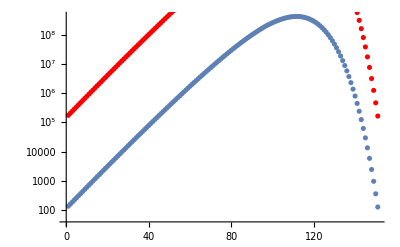

```mathematica
source=Import["/home/artem/projects/solver/build/Solve/Solvesource.txt","table"];
sol=Import["/home/artem/projects/solver/build/Solve/SolveSumIllum.txt","table"];
(*source=Flatten@Table[source[[i]],{i,170,70,-1}];*)
source=Flatten@Table[source[[i]],{i,2,Length@source}];
sol=Table[sol[[i]],{i,2,Length@sol}];
(*
sol=Flatten@Table[sol[[i]],{i,70,170}];*)
(*ListLogLogPlot[{sol,source},PlotStyle->{Red,Blue},PlotRange->{{0,1000},All}]
source=Flatten@Table[source[[i]],{i,2,500}];
sol=Flatten@Table[sol[[i]],{i,2,500}];
*)
(*Оставить этот график для приведения примеры сеточной диссипации на константе*)
Show[ListLogPlot[Table[source[[i]],{i,20,170}],PlotRange->All],
ListLogPlot[Table[sol[[i,2]],{i,20,170}],PlotRange->All,PlotStyle->Red]]
```

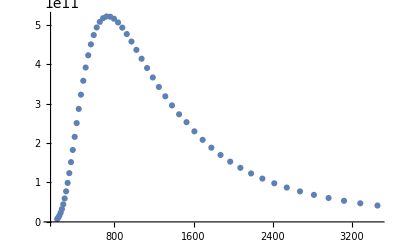

```mathematica
ListPlot[Table[{(3*10^10)/sol[[i,1]]*10^7,sol[[i,2]]},{i,100,155}],PlotRange->All]
```

```mathematica
kC = 3 * 10^10;        
kHplank = 6.62 * 10^-27;
kb = 1.3807 * 10^-16;
kStefanBoltzmann = 5.670374419 * 10^-5; 
A=(2 kb^4)/(kC^2 kHplank^3);
T=5000;
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4
```

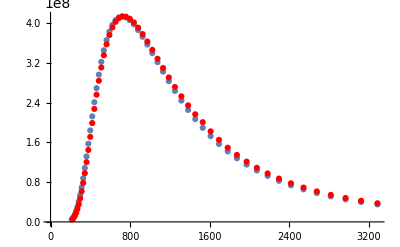

{{721.318,4.13207×10^8}}

{{721.318,4.13207×10^8}}

{{1.,1.}}

{{{222.538,5.76016×10^6},0.222328}}

```mathematica
x0=100; x1=155;normC= 1261.5723216892322;
SoLWm=Table[{kC/sol[[x+1,1]]*10^7,Ie[T,sol[[x+1,1]],sol[[x,1]]]},{x,x0,x1}]//N;
SoLCpp=Table[{kC/sol[[i,1]]*10^7,sol[[i,2]]/normC},{i,x0,x1}]//N;
Show[ListPlot[SoLWm],
ListPlot[SoLCpp,PlotRange->All,PlotStyle->Red]]

mCpp=MaximalBy[SoLCpp,Last]
mWm=MaximalBy[SoLWm,Last]
mCpp/mWm
MaximalBy[Table[{SoLCpp[[i]],Abs[Log@SoLWm[[i,2]]-Log@SoLCpp[[i,2]]]},{i,1,Length@SoLCpp}],Last]
```

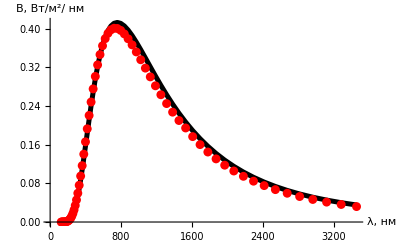

```mathematica
x0=100; x1=167;
SoLWmV=Table[{kC/sol[[x,1]]*10^7,Ie[T,sol[[x+1,1]],sol[[x,1]]]/10^9},{x,x0,x1}]//N;
SoLCppV=Table[{kC/sol[[i,1]]*10^7,sol[[i,2]]/normC/1.03/10^9},{i,x0,x1}]//N;
Show[ListLinePlot[SoLWmV,PlotStyle->Directive[Black,Thickness[0.009]],AxesStyle->Directive[Black, 12],AxesLabel->{"λ, :043d:043c","B, :0412:0442/(:043c)^2/ :043d:043c"}],
ListPlot[SoLCppV,PlotRange->All,PlotStyle->Directive[Red, PointSize[0.016]]]]
```

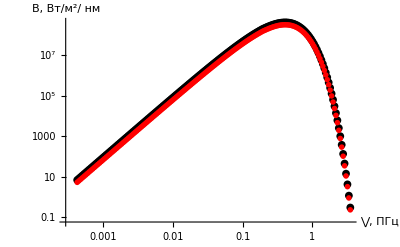

```mathematica
x0=2; x1=175;
Show[ListLogLogPlot[Table[{sol[[i,1]]/10^15,source[[i]]},{i,x0,x1}],PlotRange->All,PlotStyle->Directive[Black,PointSize[0.014]],AxesStyle->Directive[Black, 12],AxesLabel->{"⋁, :041f:0413:0446","B, Вт/(:043c)^2/ :043d:043c"}],
ListLogLogPlot[Table[{sol[[i,1]]/10^15,sol[[i,2]]/normC/1.3},{i,x0,x1}],PlotStyle->Directive[Red, PointSize[0.01]]]]
```